## Continuous IFT

Largely from https://en.wikipedia.org/wiki/Whittaker%E2%80%93Shannon_interpolation_formula and derivation from https://en.wikipedia.org/wiki/Nyquist%E2%80%93Shannon_sampling_theorem

```mathematica
x[t_]:=2Sin[t]+3Sin[4t]

B=4; (* Highest Frequency *)
fs=2B; (* Samples per Second *)
T=1/fs; (* Sample Period *)
```

```mathematica
xSamples[n_]:=T*x[n T] (* nth sample of x *)
Sincn[x_]:=Sinc[Pi x]; (* normalized sinc function *)
```

#### Formula on wikipedia:

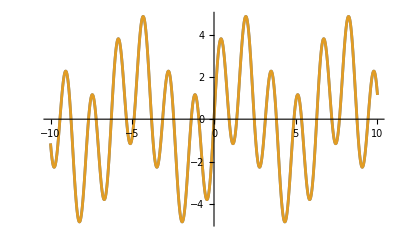

```mathematica
iftc2[t_]:=Sum[x[n T]*Sincn[(t-n T)/T], {n, -100, 100}]
Plot[{x[t],iftc2[t]}, {t, -10, 10}]
```

```mathematica
e2=NIntegrate[(x[t]-iftc2[t])^2, {t, -10, 10}, Method->"RiemannRule"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-9.71167468505009}. NIntegrate obtained 4.22733×10^-7 and 4.95343×10^-10 for the integral and error estimates.

4.22733×10^-7

#### Windowed formula:

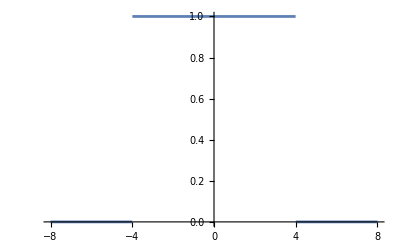

```mathematica
H[f_]:=If[Abs[f]<B, 1, 0]
Plot[H[f], {f,-2B,2B}]
```

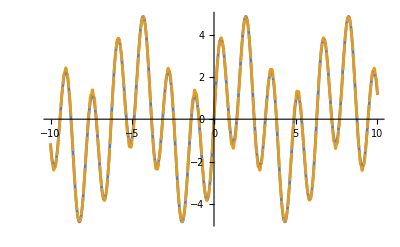

```mathematica
iftc3[t_]:=Sum[x[n T]*H[(t-n T)/T]*Sincn[(t-n T)/T], {n, -100, 100}]
Plot[{x[t],iftc3[t]}, {t, -10, 10}]
```

```mathematica
e3=NIntegrate[(x[t]-iftc3[t])^2, {t, -10, 10}, Method->"RiemannRule"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.11502}. NIntegrate obtained 0.109665 and 0.00150929 for the integral and error estimates.

0.109665

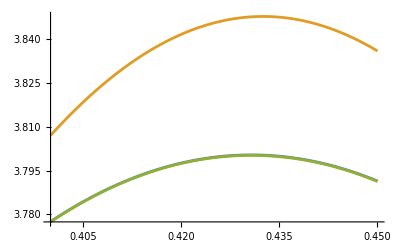

```mathematica
Plot[{x[t],iftc3[t],iftc2[t]}, {t, .4, .45}]
```

Gives a really bad approximation apparently

#### Expansion of every term of the formula

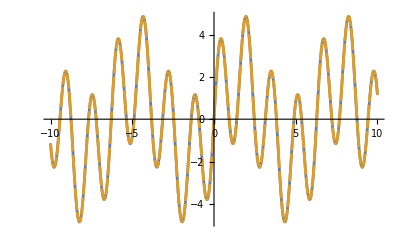

```mathematica
iftc4[t_]:=(T/Pi) Sum[x[n T]*Sin[N[Pi(t-n T)/T]]/(t-n T), {n, -100, 100}]
Plot[{x[t],iftc4[t]}, {t, -10, 10}]
```

```mathematica
e4=NIntegrate[(x[t]-iftc4[t])^2, {t, -10, 10}, Method->"RiemannRule"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-9.71167468505009}. NIntegrate obtained 4.22733×10^-7 and 4.95343×10^-10 for the integral and error estimates.

4.22733×10^-7

#### Not any improvements I can see. Hann window maybe?

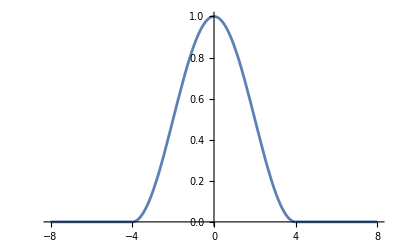

```mathematica
Hann[x_]:=HannWindow[x T]
Plot[Hann[f], {f,-2B,2B}]
```

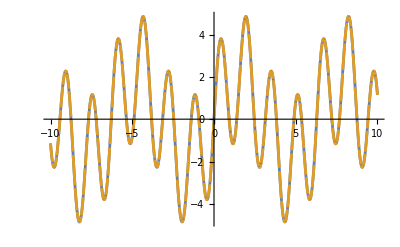

```mathematica
iftc5[t_]:=Sum[x[n T]*Hann[(t-n T)/T]*Sincn[(t-n T)/T], {n, -100, 100}]
Plot[{x[t],iftc5[t]}, {t, -10, 10}]
```

```mathematica
e5=NIntegrate[(x[t]-iftc5[t])^2, {t, -10, 10}, Method->"RiemannRule"]
```

NIntegrate`SymbolicPiecewiseSubdivision::maxpwc: The number of piecewise regions has exceeded the maximum value specified by the option MaxPiecewiseCases -> 100. The integration will continue with no piecewise subdivision.

0.

Thats encouraging...

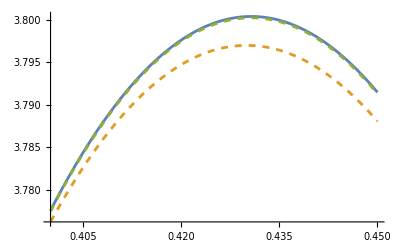

```mathematica
Plot[{x[t],Style[iftc5[t], Dashed],Style[iftc2[t], Dashed]}, {t, .4, .45}]
```

nevermind

#### Hamming window!

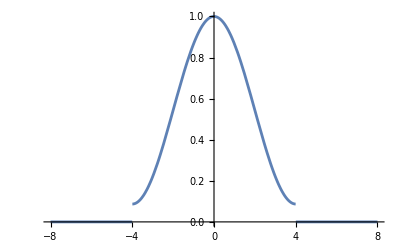

```mathematica
Hann[x_]:=HammingWindow[x T]
Plot[Hann[f], {f,-2B,2B}]
```

```mathematica
iftc6[t_]:=Sum[x[n T]*Hann[(t-n T)/T]*Sincn[(t-n T)/T], {n, -100, 100}]
Plot[{x[t],iftc6[t]}, {t, -10, 10}]
```

-Graphics-

```mathematica
e6=NIntegrate[(x[t]-iftc6[t])^2, {t, -10, 10}, Method->"RiemannRule"]
```

NIntegrate`SymbolicPiecewiseSubdivision::maxpwc: The number of piecewise regions has exceeded the maximum value specified by the option MaxPiecewiseCases -> 100. The integration will continue with no piecewise subdivision.

0.

Thats encouraging...

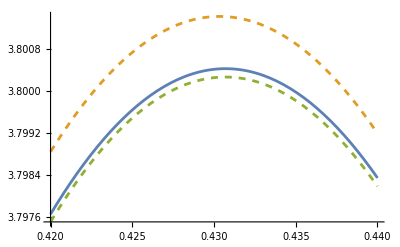

```mathematica
Plot[{x[t],Style[iftc6[t], Dashed],Style[iftc2[t], Dashed]}, {t, .42, .44}]
```

again, nevermind

#### All out

3x the samples:

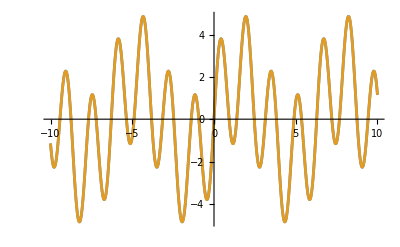

```mathematica
iftc7[t_]:=Sum[x[n T]*Sincn[(t-n T)/T], {n, -300, 300}]
Plot[{x[t],iftc7[t]}, {t, -10, 10}]
```

```mathematica
e7=NIntegrate[(x[t]-iftc7[t])^2, {t, -10, 10}, Method->"RiemannRule"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-9.57047660549127}. NIntegrate obtained 0.0000416824 and 2.7766×10^-8 for the integral and error estimates.

0.0000416824

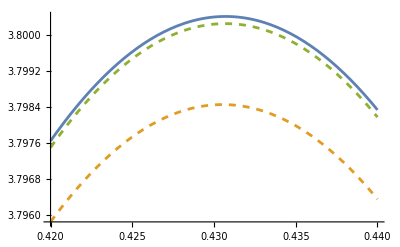

```mathematica
Plot[{x[t],Style[iftc7[t], Dashed],Style[iftc2[t], Dashed]}, {t, .42, .44}]
```

huh.

```mathematica
Manipulate[Plot[{x[t],Style[iftc7[t], Dashed],Style[iftc2[t], Dashed]}, {t, a-.002, a+.002}], {a, -10, 10}]
```

why the hell does that happen?

## Minimzation

```mathematica
poly[coef_][x_]:=Sum[coef[[i]] Cos[x * (i-1)], {i, Length[coef]}]
```

```mathematica
error[func_]:=NIntegrate[(Cos[2 Pi w]-func[w])^2, {w, -1,1}]
```

```mathematica
eFunc[coef_]:=error[poly[coef][poly[coef][#]]&]
```

```mathematica
n=6;
s=NMinimize[eFunc[Table[z[i], {i, n}]], Table[z[i], {i, n}], Method->"NelderMead"]
```

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+«4»+Cos[Times[«2»]] z[6]] z[2]-«1» «1»-«1»-Cos[4 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[5]-Cos[5 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[6])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+«4»+Cos[Times[«2»]] z[6]] z[2]-«1» «1»-«1»-Cos[4 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[5]-Cos[5 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[6])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$339+Cos[2 π w]-v2$340 Cos[v1$339+«4»+v6$344 «1»]-«1»-«1»-v5$343 Cos[4 (v1$339+v2$340 Cos[«1»]+v3$341 Cos[«1»]+v4$342 Cos[«1»]+v5$343 Cos[«1»]+v6$344 Cos[«1»])]-v6$344 Cos[5 (v1$339+v2$340 Cos[«1»]+v3$341 Cos[«1»]+v4$342 Cos[«1»]+v5$343 Cos[«1»]+v6$344 Cos[«1»])])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

{0.0144072,{z[1]→-17.0724,z[2]→14.6867,z[3]→21.3906,z[4]→-31.2455,z[5]→17.0824,z[6]→-3.88236}}

{-17.0724,14.6867,21.3906,-31.2455,17.0824,-3.88236}

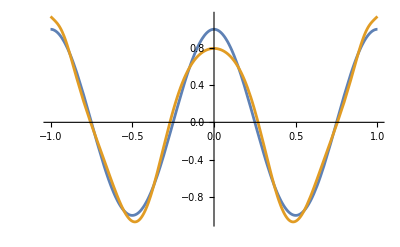

```mathematica
sol=Values[Last[s]]
solf[x_]:=poly[sol][poly[sol][x]]
Plot[{Cos[2 Pi x],solf[x]}, {x, -1,1}]
```

```mathematica
solHist={};
pHist={};
```

```mathematica
j[n_]:=(
s=NMinimize[eFunc[Table[z[i], {i, n}]], Table[z[i], {i, n}], Method->"NelderMead"];
sol=Values[Last[s]];
AppendTo[solHist, sol];
solf[x_]:=poly[sol][poly[sol][x]];
Last[AppendTo[pHist,Labeled[Plot[{Cos[2 Pi x],solf[x]}, {x, -1,1}], n]]]
)
```

```mathematica
j/@Range[1, 10]
```

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$473+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+Cos[w] z[2]] z[2])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$476+Cos[2 π w]-v2$477 Cos[v1$476+v2$477 Cos[w]])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+Cos[w] z[2]+Cos[Times[«2»]] z[3]] z[2]-Cos[2 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[3])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$480+Cos[2 π w]-v2$481 Cos[v1$480+v2$481 Cos[w]+v3$482 Cos[Times[«2»]]]-v3$482 Cos[2 (v1$480+v2$481 Cos[«1»]+v3$482 Cos[«1»])])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+Cos[w] z[2]+Cos[Times[«2»]] z[3]+Cos[Times[«2»]] z[4]] z[2]-Cos[2 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[3]-Cos[3 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[4])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$485+Cos[2 π w]-v2$486 Cos[v1$485+v2$486 Cos[w]+v3$487 Cos[Times[«2»]]+v4$488 Cos[Times[«2»]]]-v3$487 Cos[2 (v1$485+v2$486 Cos[«1»]+v3$487 Cos[«1»]+v4$488 Cos[«1»])]-v4$488 Cos[3 (v1$485+v2$486 Cos[«1»]+v3$487 Cos[«1»]+v4$488 Cos[«1»])])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+Cos[w] z[2]+Cos[«1»] «1»+Cos[Times[«2»]] z[4]+Cos[Times[«2»]] z[5]] «1»-«1»-Cos[3 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[4]-Cos[4 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[5])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$491+Cos[2 π w]-v2$492 Cos[v1$491+«3»+v5$495 Cos[Times[«2»]]]-v3$493 Cos[2 («1»)]-v4$494 Cos[3 (v1$491+v2$492 Cos[«1»]+v3$493 Cos[«1»]+v4$494 Cos[«1»]+v5$495 Cos[«1»])]-v5$495 Cos[4 (v1$491+v2$492 Cos[«1»]+v3$493 Cos[«1»]+v4$494 Cos[«1»]+v5$495 Cos[«1»])])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-Cos[z[1]+«4»+Cos[Times[«2»]] z[6]] z[2]-«1» «1»-«1»-Cos[4 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[5]-Cos[5 (z[1]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»]+Cos[«1»] z[«1»])] z[6])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$498+Cos[2 π w]-v2$499 Cos[v1$498+«4»+v6$503 «1»]-«1»-«1»-v5$502 Cos[4 (v1$498+v2$499 Cos[«1»]+v3$500 Cos[«1»]+v4$501 Cos[«1»]+v5$502 Cos[«1»]+v6$503 Cos[«1»])]-v6$503 Cos[5 (v1$498+v2$499 Cos[«1»]+v3$500 Cos[«1»]+v4$501 Cos[«1»]+v5$502 Cos[«1»]+v6$503 Cos[«1»])])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand («1»)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$506+«13»)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

$Aborted

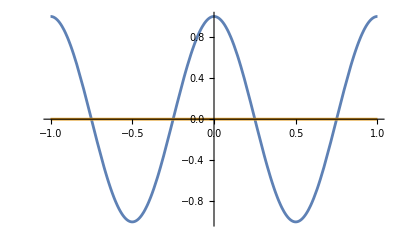
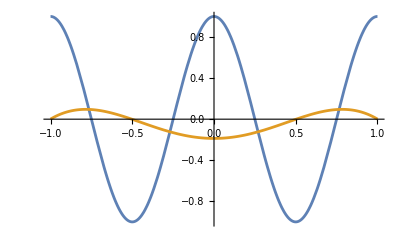
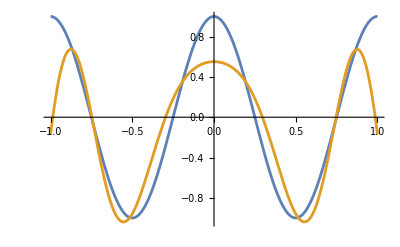
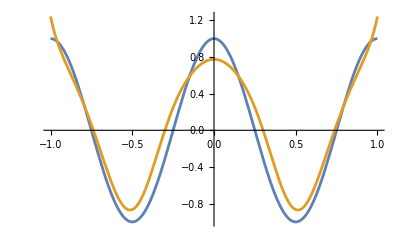
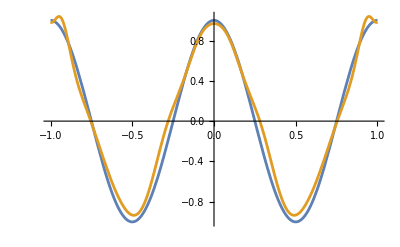
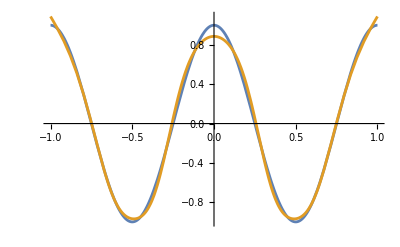
{-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7}

```mathematica
pHist
```

```mathematica
Last[pHist]
```

-Graphics-7

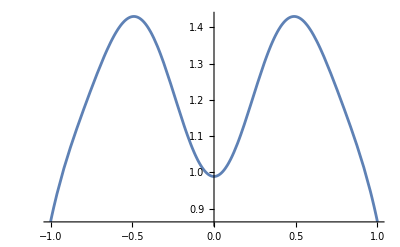

```mathematica
Plot[poly[sol][z], {z, -1, 1}]
```

```mathematica
poly[sol][x]
```

-7.85376+18.8849 Cos[x]-20.7173 Cos[2 x]+20.7124 Cos[3 x]-15.443 Cos[4 x]+7.22408 Cos[5 x]-1.81838 Cos[6 x]